```mathematica
1+1
```

2

```mathematica
F[x_]=DSolve[{y'[x]-y[x]^2==x^2,y[0]==1/2},y[x],x][[1,1,2]]//Simplify
```

(-x^2 BesselJ[-3/4,x^2/2] Gamma[1/4]+2 (x^2 BesselJ[-5/4,x^2/2]+BesselJ[-1/4,x^2/2]-x^2 BesselJ[3/4,x^2/2]) Gamma[3/4])/(x (BesselJ[1/4,x^2/2] Gamma[1/4]-4 BesselJ[-1/4,x^2/2] Gamma[3/4]))

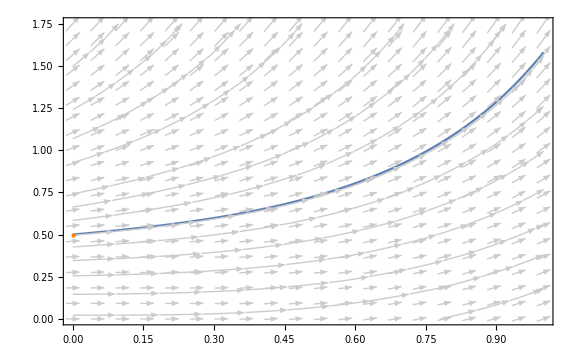

```mathematica
Show[
Plot[F[x],{x,0,1},PlotRange->{{0,1},{0,1.75}},
Epilog->{Orange,PointSize[Medium],Point[{0,1/2}]},
ImageSize->Large,LabelStyle->Medium,Frame->True
],
VectorPlot[{1,x^2+y^2},{x,0,1},{y,0,1.75},
VectorPoints->20,VectorScale->Small,StreamPoints->Coarse,
VectorStyle->RGBColor[0.8,0.8,0.8],StreamStyle->RGBColor[0.8,0.8,0.8]
]
]
```

```mathematica
G[x_,y_]:=x^2+y^2
```

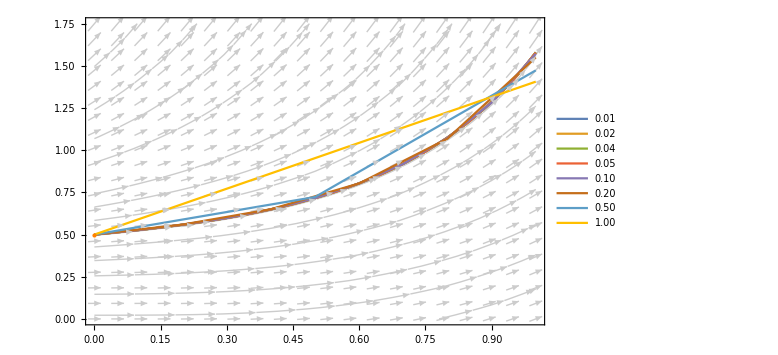

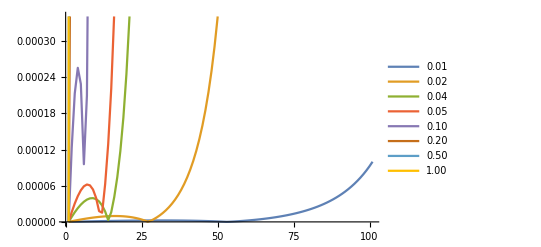

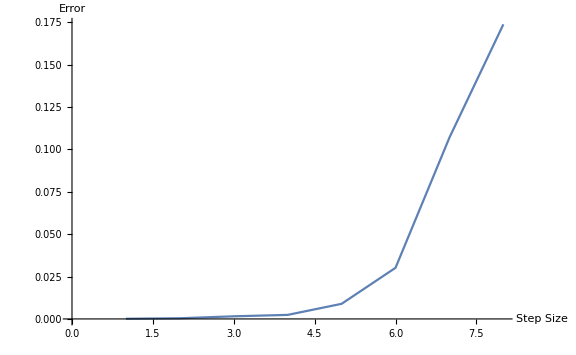

{0.0000631297,0.000250121,0.000979138,0.00151179,0.00564529,0.0190968,0.0677348,0.110016}

```mathematica
Order2[h_]:=Module[{StepSize},
StepSize=h;Points={};xx=0;yy=1/2;Error={};
For[xx=0,xx≤1,xx=xx+StepSize,
AppendTo[Points,{xx,yy}];
AppendTo[Error,Abs[yy-If[xx==0,1/2,F[xx]]]];
k1=G[xx,yy];
k2=G[xx+StepSize,yy+StepSize*k1];
yy=yy+0.5*StepSize*(k1+k2);
];
Return[{Points,Error}]
]

SS01=Order2[0.01];
SS02=Order2[0.02];
SS04=Order2[0.04];
SS05=Order2[0.05];
SS10=Order2[0.10];
SS20=Order2[0.20];
SS50=Order2[0.50];
SS00=Order2[1.00];
Show[
Plot[F[x],{x,0,1},PlotRange->{{0,1},{0,1.75}},
Epilog->{Orange,PointSize[Medium],Point[{0,1/2}]},
ImageSize->Large,LabelStyle->Medium,Frame->True
],
VectorPlot[{1,x^2+y^2},{x,0,1},{y,0,1.75},
VectorPoints->20,VectorScale->Small,StreamPoints->Coarse,
VectorStyle->RGBColor[0.8,0.8,0.8],StreamStyle->RGBColor[0.8,0.8,0.8]
],
ListPlot[{SS01[[1]],SS02[[1]],SS04[[1]],SS05[[1]],SS10[[1]],SS20[[1]],SS50[[1]],SS00[[1]]},Joined->True,PlotLegends->{"0.01","0.02","0.04","0.05","0.10","0.20","0.50","1.00"}]
]
ListPlot[{SS01[[2]],SS02[[2]],SS04[[2]],SS05[[2]],SS10[[2]],SS20[[2]],SS50[[2]],SS00[[2]]},Joined->True,PlotLegends->{"0.01","0.02","0.04","0.05","0.10","0.20","0.50","1.00"}]
Es={SS01[[2]][[-1]],SS02[[2]][[-1]],SS04[[2]][[-1]],SS05[[2]][[-1]],SS10[[2]][[-1]],SS20[[2]][[-1]],SS50[[2]][[-1]],SS00[[2]][[-1]]};
ListPlot[Es,
Joined->True,AxesLabel->{"Step Size","Error"},ImageSize->Large,LabelStyle->Medium]
Es/F[1]
```

```mathematica
Order3[h_,a_,b_]:=Module[{StepSize,A,B},
StepSize=h;A=a;B=b;Points={};xx=0;yy=1/2;Error={};
For[xx=0,xx≤1+0.001,xx=xx+StepSize,
AppendTo[Points,{xx,yy}];
AppendTo[Error,Abs[yy-If[xx==0,1/2,F[xx]]]];
k1=G[xx,yy];
k2=G[xx+A[[1]]*StepSize,yy+A[[2]]*StepSize*k1];
k3=G[xx+A[[3]]*StepSize,yy+A[[4]]*StepSize*k1+A[[5]]*StepSize*k2];
yy=yy+StepSize*(B[[1]]*k1+B[[2]]*k2+B[[3]]*k3);
];
Return[{Points,Error}]
]
Order4[h_,a_,b_]:=Module[{StepSize,A,B},
StepSize=h;A=a;B=b;Points={};xx=0;yy=1/2;Error={};
For[xx=0,xx≤1+0.001,xx=xx+StepSize,
AppendTo[Points,{xx,yy}];
AppendTo[Error,Abs[yy-If[xx==0,1/2,F[xx]]]];
k1=G[xx,yy];
k2=G[xx+A[[1]]*StepSize,yy+A[[2]]*StepSize*k1];
k3=G[xx+A[[3]]*StepSize,yy+A[[4]]*StepSize*k1+A[[5]]*StepSize*k2];
k4=G[xx+A[[6]]*StepSize,yy+A[[7]]*StepSize*k1+A[[8]]*StepSize*k2+A[[9]]*StepSize*k3];
yy=yy+StepSize*(B[[1]]*k1+B[[2]]*k2+B[[3]]*k3+B[[4]]*k4);
];
Return[{Points,Error}]
]
```

```mathematica
Data={Order2[0.1],
Order3[0.1,{1/2,1/2,1,-1,2},{1/6,2/3,1/6}],
Order3[0.1,{1/3,1/3,2/3,0,2/3},{1/4,0,3/4}],
Order3[0.1,{1/2,1/2,3/4,0,3/4},{2/9,1/3,4/9}],
Order4[0.1,{1/2,1/2,1/2,0,1/2,1,0,0,1},{1/6,1/3,1/3,1/6}],
Order4[0.1,{1/3,1/3,2/3,1/3,1,1,1,-1,1},{1/8,3/8,3/8,1/8}]};
```

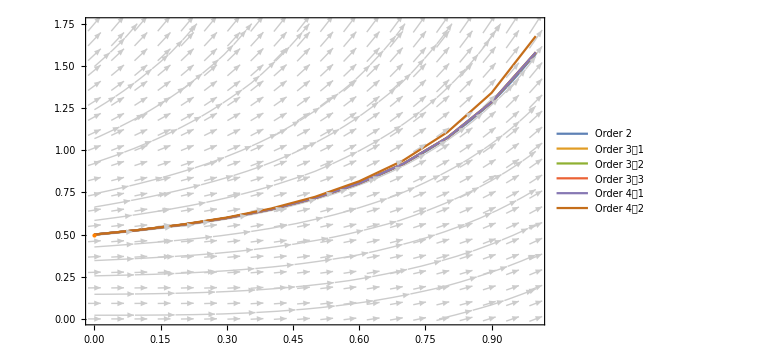

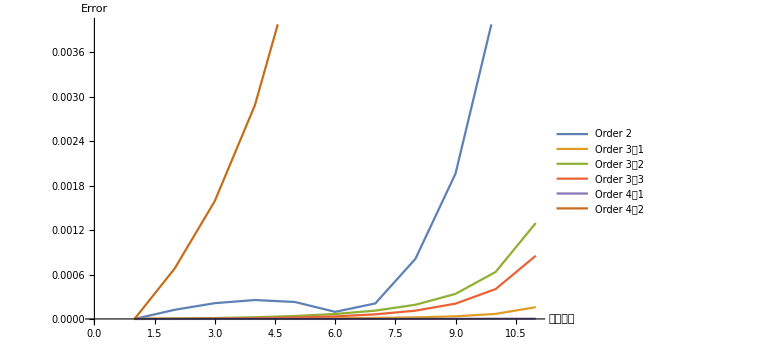

{0.00564529,0.000100704,0.000819787,0.000540382,1.9176×10^-6,0.0607347}

```mathematica
Legends={"Order 2","Order 3，1","Order 3，2","Order 3，3","Order 4，1","Order 4，2"};
Show[
Plot[F[x],{x,0,1},PlotRange->{{0,1},{0,1.75}},
Epilog->{Orange,PointSize[Medium],Point[{0,1/2}]},
ImageSize->Large,LabelStyle->Medium,Frame->True
],
VectorPlot[{1,x^2+y^2},{x,0,1},{y,0,1.75},
VectorPoints->20,VectorScale->Small,StreamPoints->Coarse,
VectorStyle->RGBColor[0.8,0.8,0.8],StreamStyle->RGBColor[0.8,0.8,0.8]
],
ListPlot[Table[Data[[i]][[1]],{i,1,6}],Joined->True,PlotLegends->Legends]
]
Es=Table[Data[[i]][[2]],{i,1,6}];
ListPlot[Es,
Joined->True,AxesLabel->{"迭代次数","Error"},ImageSize->Large,LabelStyle->Medium,PlotLegends->Legends]
Table[Data[[i]][[2]][[-1]],{i,1,6}]/F[1]
```

```mathematica
A={1/2,1/2,1,-1,2};
B={1/6,2/3,1/6};
Points={};xx=0;yy=1/2;Error={};
StepSize=0.1;
```

```mathematica
For[xx=0,xx≤1+0.001,xx=xx+StepSize,
AppendTo[Points,{xx,yy}];
AppendTo[Error,Abs[yy-If[xx==0,1/2,F[xx]]]];
k1=G[xx,yy];
k2=G[xx+A[[1]]*StepSize,yy+A[[2]]*StepSize*k1];
k3=G[xx+A[[3]]*StepSize,yy+A[[4]]*StepSize*k1+A[[5]]*StepSize*k2];
yy=yy+StepSize*(B[[1]]*k1+B[[2]]*k2+B[[3]]*k3);
Print[xx]
];
```

0

0.1

0.2

0.3

0.4

0.5

0.6

0.7

0.8

0.9

1.

```mathematica
Data[[1]]
```

{{{0,1/2},{0.1,0.526781},{0.2,0.558587},{0.3,0.598317},{0.4,0.649396},{0.5,0.716015},{0.6,0.803534},{0.7,0.919187},{0.8,1.07334},{0.9,1.28189},{1.,1.57116}},{0,0.000123261,0.000213022,0.000255486,0.000228673,0.0000956488,0.000209395,0.000811211,0.0019628,0.00421902,0.00892005}}

```mathematica
Order3[0.1,{1/2,1/2,1,-1,2},{1/6,2/3,1/6}]
```

Part::partw: Part 4 of {1/6,2/3,1/6} does not exist.

Part::partw: Part 5 of {1/6,2/3,1/6} does not exist.

Part::partd: Part specification c⟦1⟧ is longer than depth of object.

Part::partd: Part specification c⟦2⟧ is longer than depth of object.

Part::partd: Part specification c⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 4 of {1/6,2/3,1/6} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted[]

```mathematica
1+2
```

```mathematica
Data2={
Order4[0.01,{1/2,1/2,1/2,0,1/2,1,0,0,1},{1/6,1/3,1/3,1/6}],
Order4[0.02,{1/2,1/2,1/2,0,1/2,1,0,0,1},{1/6,1/3,1/3,1/6}],
Order4[0.04,{1/2,1/2,1/2,0,1/2,1,0,0,1},{1/6,1/3,1/3,1/6}],
Order4[0.05,{1/2,1/2,1/2,0,1/2,1,0,0,1},{1/6,1/3,1/3,1/6}],
Order4[0.10,{1/2,1/2,1/2,0,1/2,1,0,0,1},{1/6,1/3,1/3,1/6}],
Order4[0.20,{1/2,1/2,1/2,0,1/2,1,0,0,1},{1/6,1/3,1/3,1/6}],
Order4[0.50,{1/2,1/2,1/2,0,1/2,1,0,0,1},{1/6,1/3,1/3,1/6}],
Order4[1.00,{1/2,1/2,1/2,0,1/2,1,0,0,1},{1/6,1/3,1/3,1/6}]
};
```

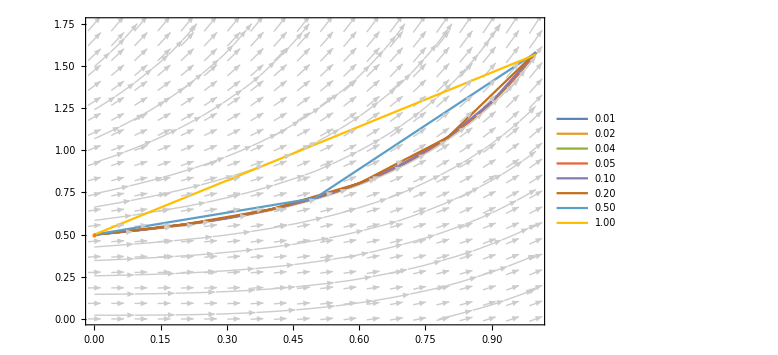

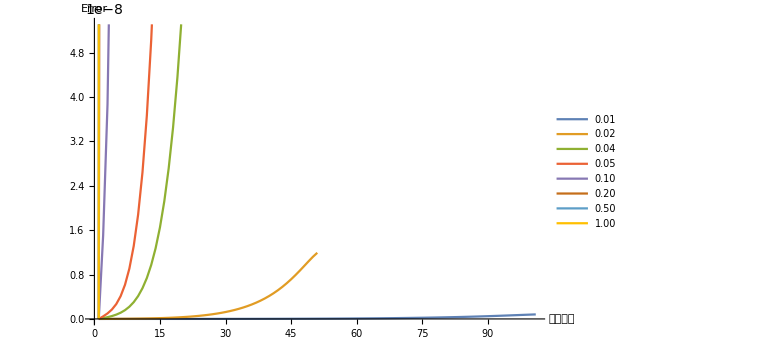

{8.15416×10^-10,1.19256×10^-8,1.5764×10^-7,3.47527×10^-7,3.02998×10^-6,3.26726×10^-6,0.00161608,0.0131257}

```mathematica
Legends2={"0.01","0.02","0.04","0.05","0.10","0.20","0.50","1.00"};
Show[
Plot[F[x],{x,0,1},PlotRange->{{0,1},{0,1.75}},
Epilog->{Orange,PointSize[Medium],Point[{0,1/2}]},
ImageSize->Large,LabelStyle->Medium,Frame->True
],
VectorPlot[{1,x^2+y^2},{x,0,1},{y,0,1.75},
VectorPoints->20,VectorScale->Small,StreamPoints->Coarse,
VectorStyle->RGBColor[0.8,0.8,0.8],StreamStyle->RGBColor[0.8,0.8,0.8]
],
ListPlot[Table[Data2[[i]][[1]],{i,1,8}],Joined->True,PlotLegends->Legends2]
]
Es=Table[Data2[[i]][[2]],{i,1,8}];
ListPlot[Es,
Joined->True,AxesLabel->{"迭代次数","Error"},ImageSize->Large,LabelStyle->Medium,PlotLegends->Legends2]
Table[Data2[[i]][[2]][[-1]],{i,1,8}]
```